Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
(* Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]; *)
<<"IGraphM`"
```

```mathematica
data=Import["../data/ccm_manipulated_396096_partitioned_in_time_windows.mx",HeaderLines->1];
```

```mathematica
Print["Weight Zero Rows: ",Length@Position[data[[10]][[All,11]],0]]
Print["Thickness + Width + Length Zero Rows: ",Length@Position[data[[10]][[All,9]],0]]
Print["Usable Rows: ",Length@data[[10]]-Length@Position[data[[10]][[All,9]],0]]
```

Weight Zero Rows: 0

Thickness + Width + Length Zero Rows: 0

Usable Rows: 396096

Investigation of Constraints Impact in Time Windows

Girvan & Newman Modularity

```mathematica
,
```

```mathematica
,
```

```mathematica
GirvanNewmanmodularity[xx_]:=Module[{network,m,Aij,B,u,β,s,Q,div1,div2,moditer,r1,r11,r12,r2,r21,r22,subfinal1Q,subfinal2Q,finalQ},
network=xx;
m=EdgeCount@network;
Aij=AdjacencyMatrix@network;
B=N@(Aij-Outer[Times,VertexDegree@network,VertexDegree@network]/(2*m));
u=Eigenvectors@B;
β=Eigenvalues@B;
s=(u/.x_/;x<0->-1)/.x_/;x≥0->1;
Q=(Total@(Table[(u[[i]].Flatten@s[[Flatten@Position[β,Max@β][[1]]]])^2,{i,VertexList@network}]*β))/(4*m);
div1=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Negative];
div2=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Positive];
moditer[pos_,B1_]:=Module[{Bg,ug,βg,sg,deltaQ,divv1,divv2,Bg1,Bg2},
Bg=(Table[B1[[i,j]]-KroneckerDelta[i,j]*Total@B1[[i,pos]],{i,Length@B1},{j,Length@B1}])[[pos,pos]];
ug=Eigenvectors@Bg;
βg=Eigenvalues@Bg;
sg=(ug/.x_/;x<0->-1)/.x_/;x≥0->1;
deltaQ=(Total@(Table[(ug[[i]].Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]])^2,{i,Range@Length@pos}]*βg))/(4*m);
divv1=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Negative];
divv2=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Positive];{deltaQ,divv1,divv2,Bg}];
r1=moditer[div1,B];
r11=If[r1[[1]]>0.001,moditer[r1[[2]],r1[[4]]],{0,0,0,0}];
r12=If[r1[[1]]>0.001,moditer[r1[[3]],r1[[4]]],{0,0,0,0}];
r2=moditer[div2,B];
r21=If[r2[[1]]>0.001,moditer[r2[[2]],r2[[4]]],{0,0,0,0}];
r22=If[r2[[1]]>0.001,moditer[r2[[3]],r2[[4]]],{0,0,0,0}];
subfinal1Q=If[r1[[1]]>0.001,If[r11[[1]]>0.001,If[r12[[1]]>0.001,r12[[1]]+r11[[1]]+r1[[1]],r11[[1]]+r1[[1]]],If[r12[[1]]>0.001,r12[[1]]+r1[[1]],r1[[1]]]],0];
subfinal2Q=If[r2[[1]]>0.001,If[r21[[1]]>0.001,If[r22[[1]]>0.001,r22[[1]]+r21[[1]]+r2[[1]],r21[[1]]+r2[[1]]],If[r22[[1]]>0.001,r22[[1]]+r2[[1]],r2[[1]]]],0];
finalQ=Q+subfinal1Q+subfinal2Q]
```

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,15,10];]
```

{342.845,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

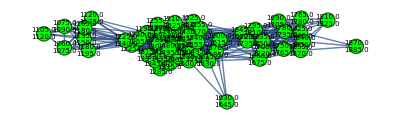
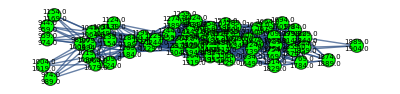
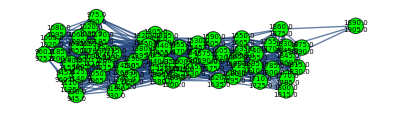
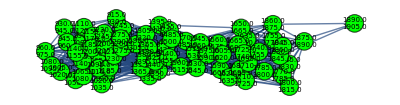
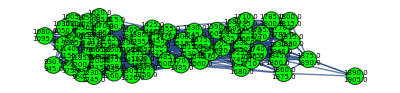
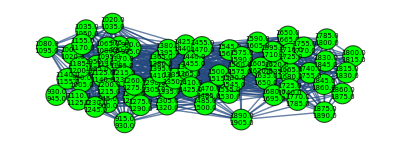
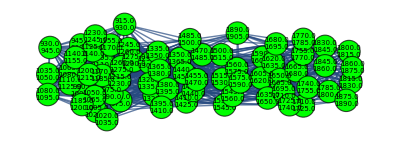
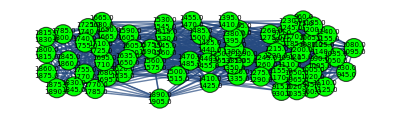
{{-Graphics-,52},{-Graphics-,63},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,67}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphs=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomGNmodularityvalues=Table[GirvanNewmanmodularity[singlerandomgraphs[[i]]],{i,Length@singlerandomgraphs}];
```

```mathematica
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Zscoremodularity=Table[randomnessfunctionformodularity[i,1],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,2,2,2,2,2,2,3}

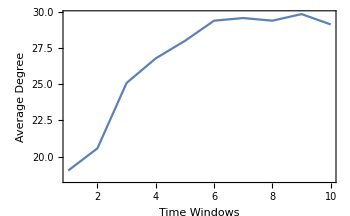
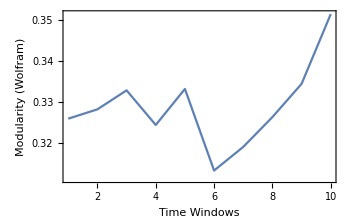
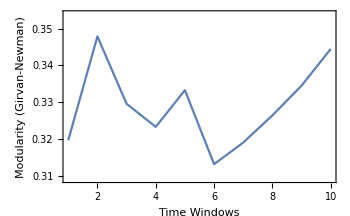
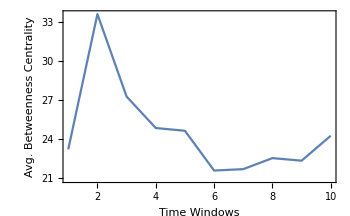
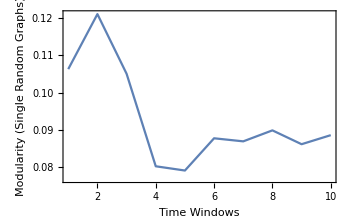
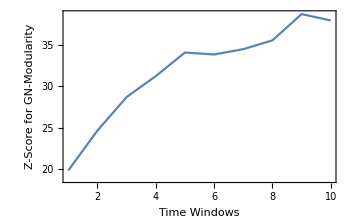

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{1,10},{0.309,0.354}}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,singlerandomGNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,Zscoremodularity[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity"},ImageSize->350,PlotRange->{{1,10},{17.5,40}}]}
```

```mathematica
Zscoremodularityswitch=Table[randomnessfunctionformodularity[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

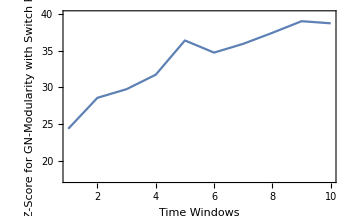

```mathematica
ListLinePlot[Thread[{Range@10,Zscoremodularityswitch[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity with Switch Rnd."},ImageSize->350,PlotRange->{{1,10},{17.5,40}}]
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[10,0.2,10];]
```

{617.113,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep[[1]][[i]],thicknessdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

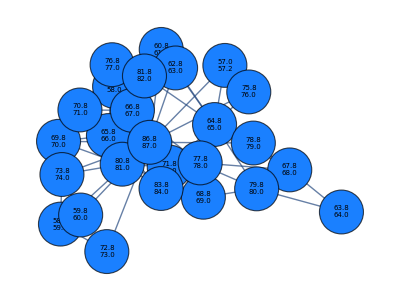
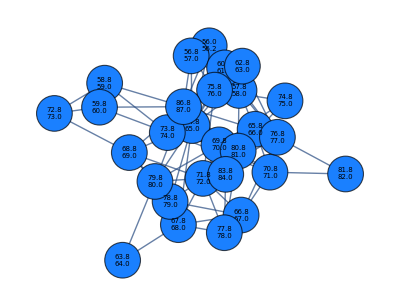
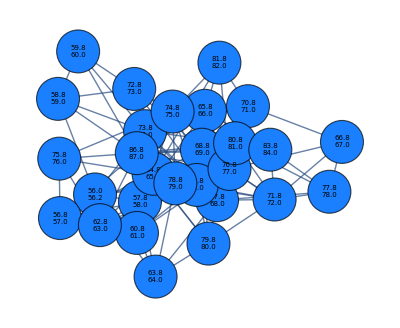
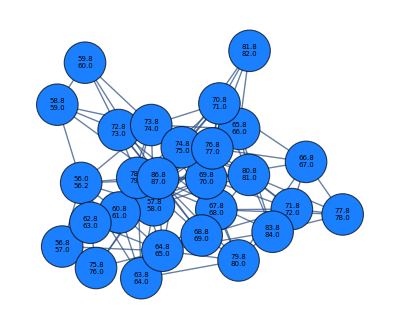
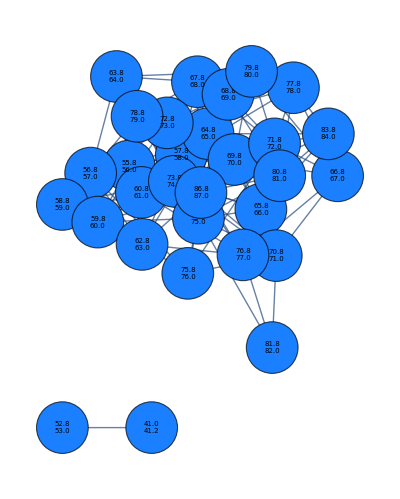
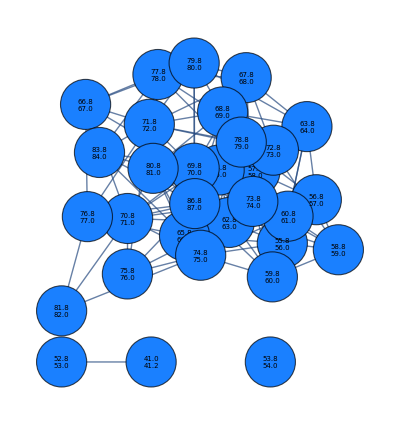
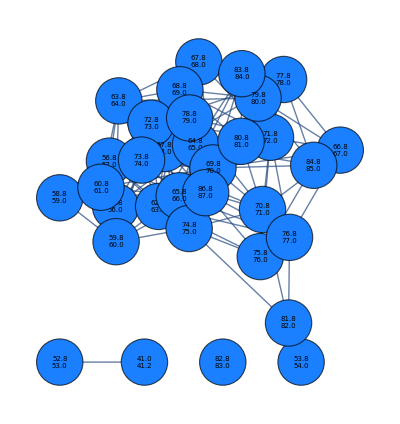
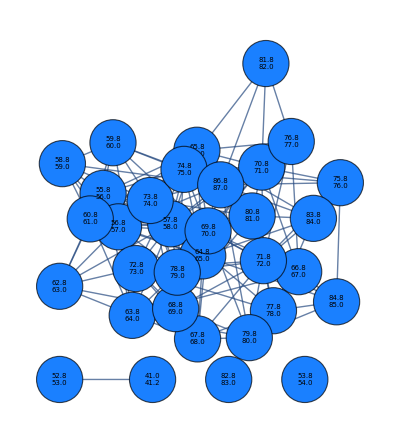
{{-Graphics-,26},{-Graphics-,28},{-Graphics-,28},{-Graphics-,28},{-Graphics-,30},{-Graphics-,31},{-Graphics-,33},{-Graphics-,33},{-Graphics-,35},{-Graphics-,35}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphs=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomGNmodularityvalues=Table[GirvanNewmanmodularity[singlerandomgraphs[[i]]],{i,Length@singlerandomgraphs}];
```

```mathematica
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Zscoremodularity=Table[randomnessfunctionformodularity[i,1],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{4,4,4,4,4,4,6,5,5,4}

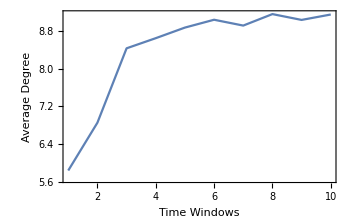
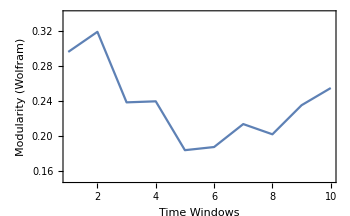
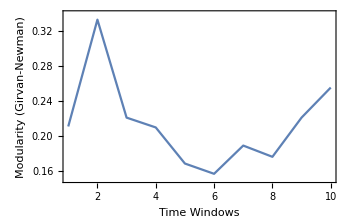
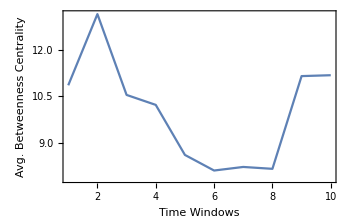
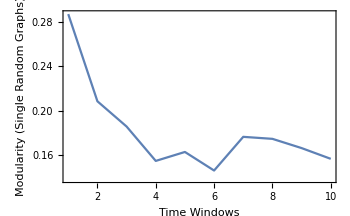
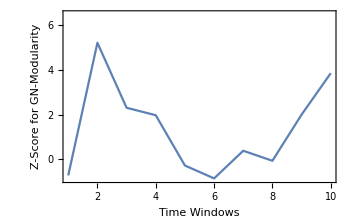

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},{0.15,0.34}}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{1,10},{0.15,0.34}}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,singlerandomGNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,Zscoremodularity[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity"},ImageSize->350,PlotRange->{{1,10},{-0.9,6.5}}]}
```

```mathematica
Zscoremodularityswitch=Table[randomnessfunctionformodularity[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

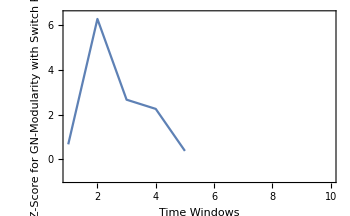

```mathematica
ListLinePlot[Thread[{Range@10,Zscoremodularityswitch[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity with Switch Rnd."},ImageSize->350,PlotRange->{{1,10},{-0.9,6.5}}]
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[12,600,10];]
```

{229.445,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedstep[[1]][[i]],lengthdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
```

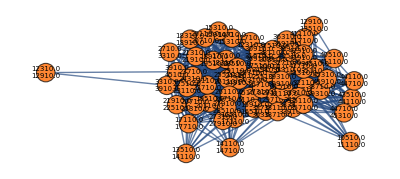
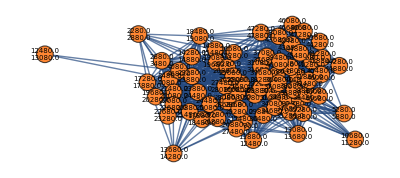
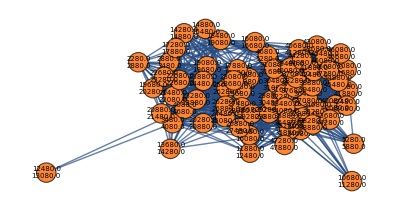
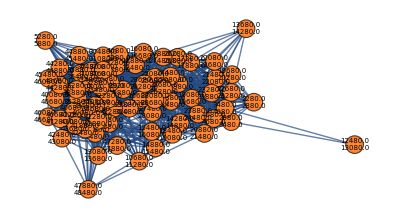
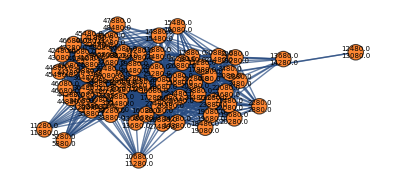
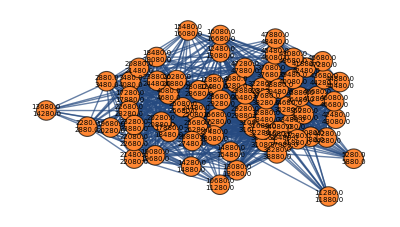
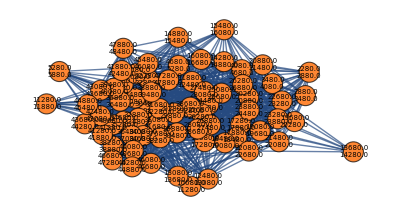
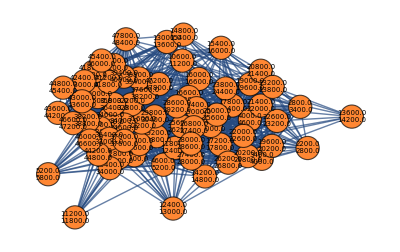
{{-Graphics-,61},{-Graphics-,67},{-Graphics-,67},{-Graphics-,68},{-Graphics-,69},{-Graphics-,69},{-Graphics-,69},{-Graphics-,69},{-Graphics-,70},{-Graphics-,70}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

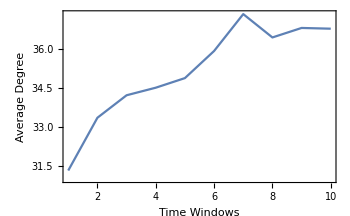
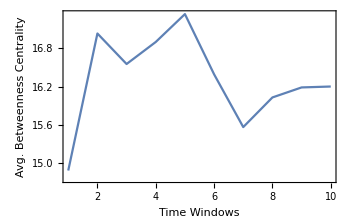
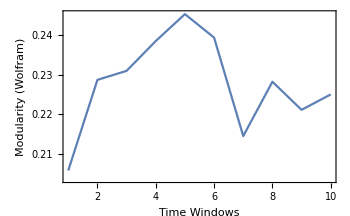
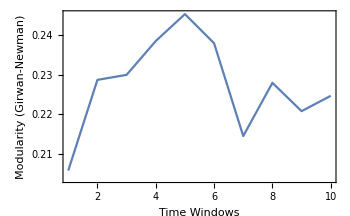

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[11,600,10];]
```

{164.225,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedstep[[1]][[i]],weightdataintimewindowsFixedstep[[2]][[i]],2,7,400,Red],{i,Range@10}];
```

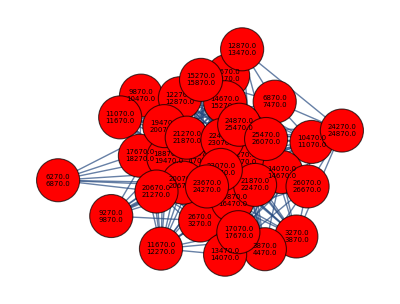
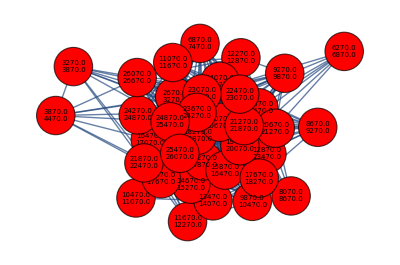
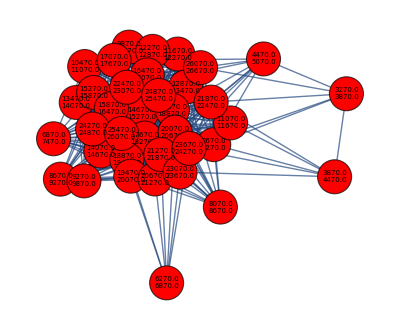
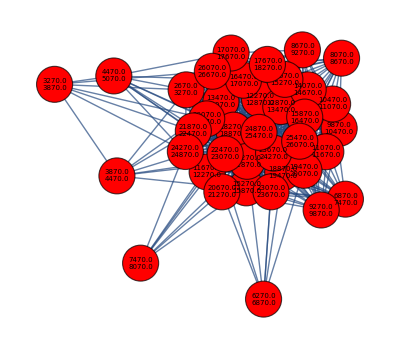
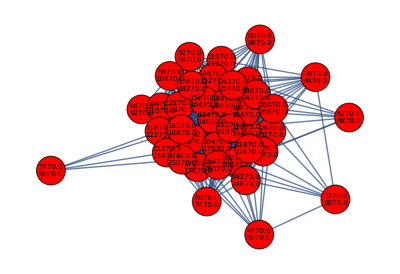
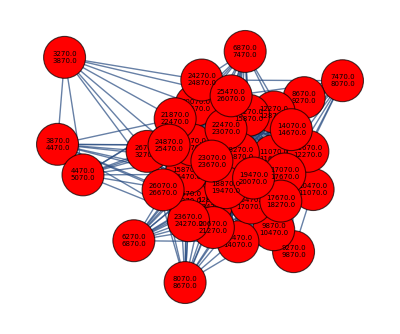
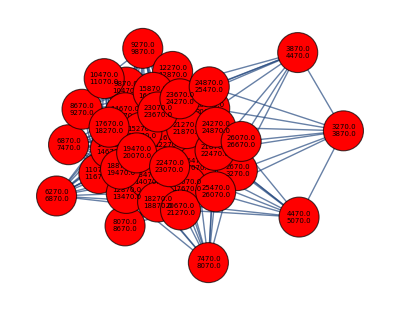
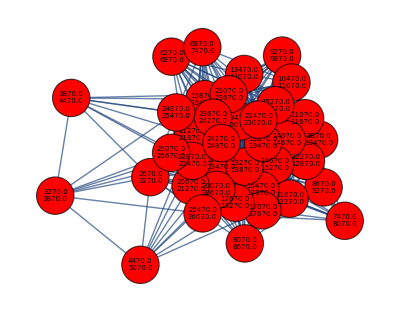
{{-Graphics-,35},{-Graphics-,36},{-Graphics-,37},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,3,2,2,2,2,2,2}

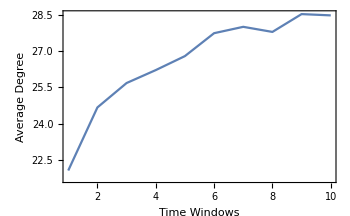
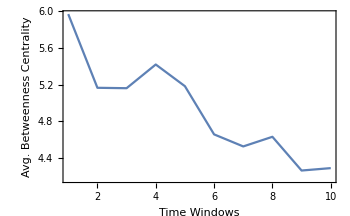
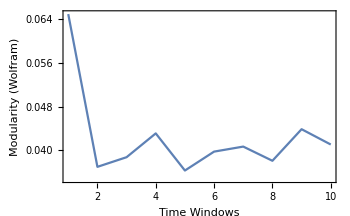
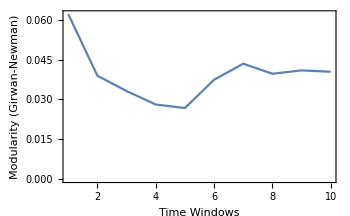

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[9,60,10];]
```

{992.259,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket[[1]][[i]],widthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Green],{i,Range@10}];
```

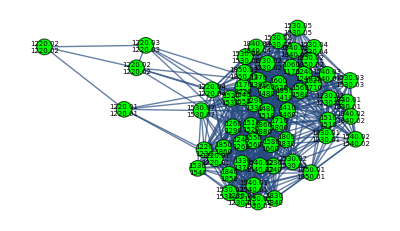
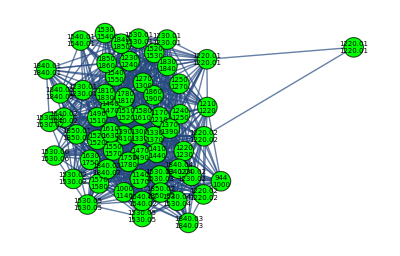
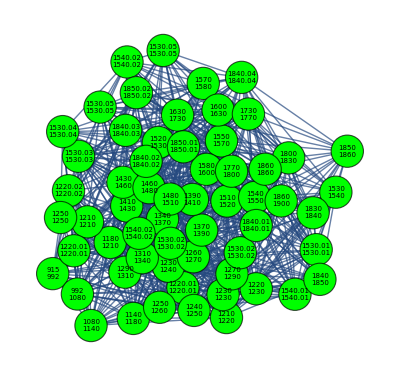
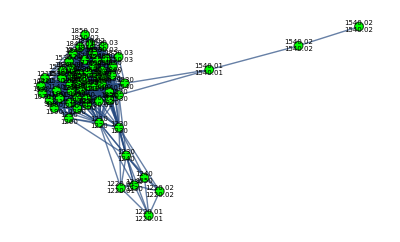
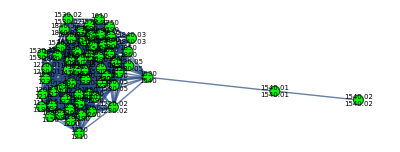
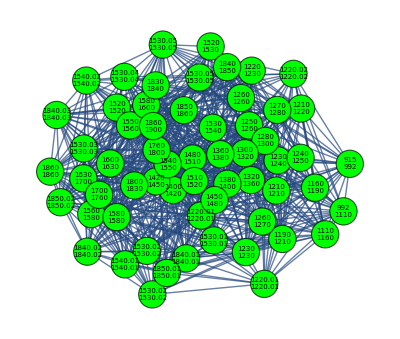
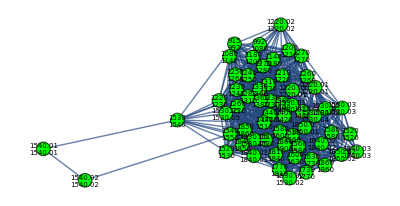
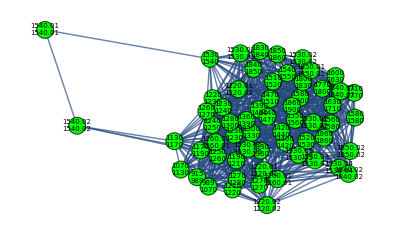
{{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphs=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomGNmodularityvalues=Table[GirvanNewmanmodularity[singlerandomgraphs[[i]]],{i,Length@singlerandomgraphs}];
```

```mathematica
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Zscoremodularity=Table[randomnessfunctionformodularity[i,1],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,3,2,3,3,2,2,3,2,2}

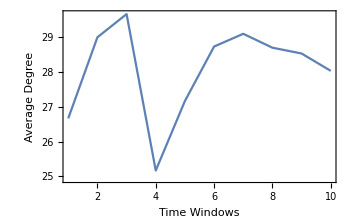
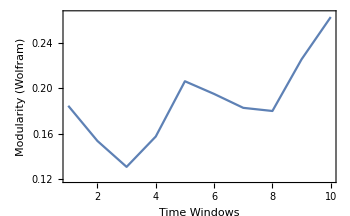
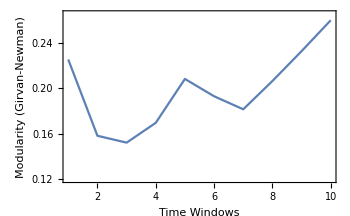
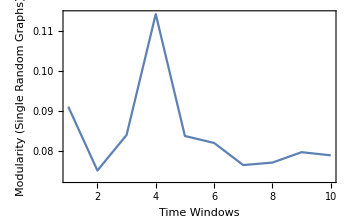
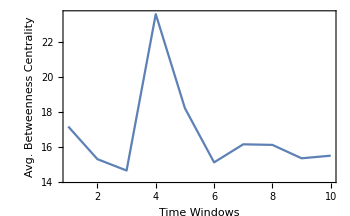
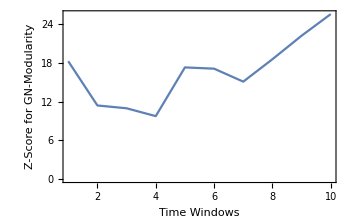

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},{0.12,0.265}}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{1,10},{0.12,0.265}}],ListLinePlot[Thread[{Range@10,singlerandomGNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,Zscoremodularity[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity"},ImageSize->350,PlotRange->{{1,10},All}]}
```

```mathematica
Zscoremodularityswitch=Table[randomnessfunctionformodularity[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

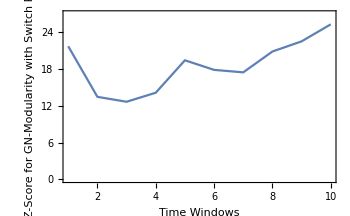

```mathematica
ListLinePlot[Thread[{Range@10,Zscoremodularityswitch[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity with Switch Rnd."},ImageSize->350,PlotRange->{{1,10},{0,27}}]
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[10,32,10];]
```

{3094.31,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket[[1]][[i]],thicknessdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

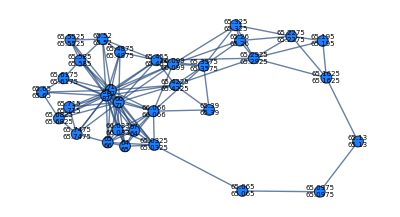
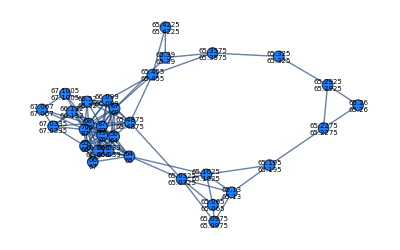
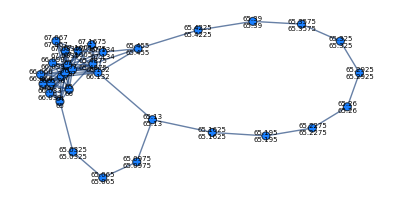
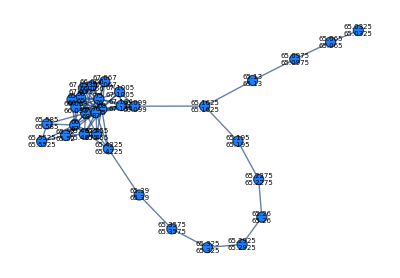
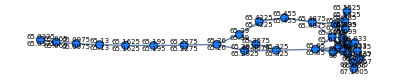
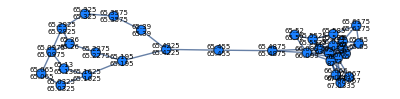
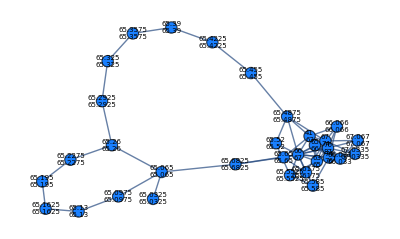
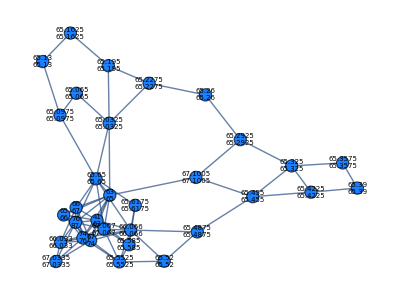
{{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphs=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomGNmodularityvalues=Table[GirvanNewmanmodularity[singlerandomgraphs[[i]]],{i,Length@singlerandomgraphs}];
```

```mathematica
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Zscoremodularity=Table[randomnessfunctionformodularity[i,1],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,4,3,4,4,4,4,4,4,4}

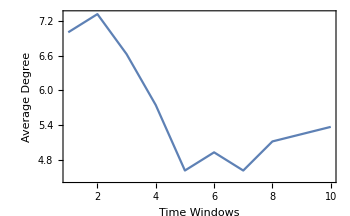
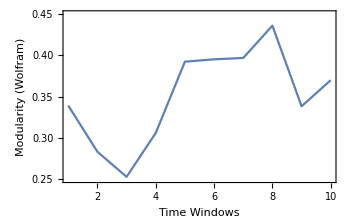
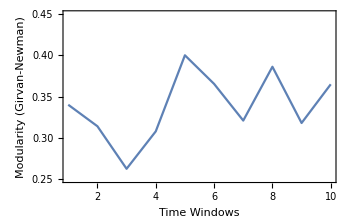
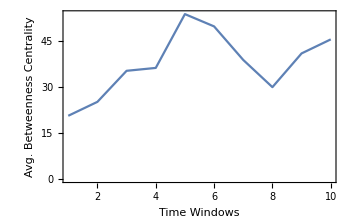
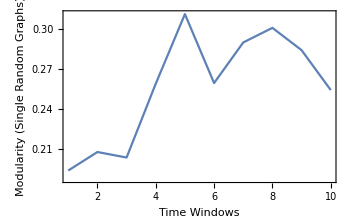
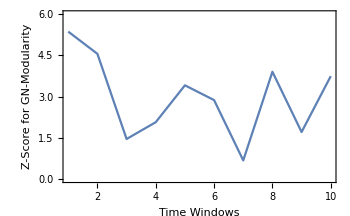

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},{0.25,0.45}}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{1,10},{0.25,0.45}}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,singlerandomGNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,Zscoremodularity[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity"},ImageSize->350,PlotRange->{{1,10},{0,6}}]}
```

```mathematica
Zscoremodularityswitch=Table[randomnessfunctionformodularity[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

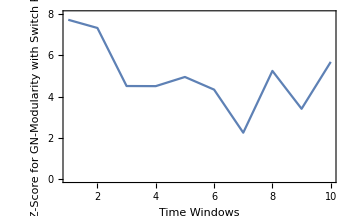

```mathematica
ListLinePlot[Thread[{Range@10,Zscoremodularityswitch[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity with Switch Rnd."},ImageSize->350,PlotRange->{{1,10},{0,8}}]
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[12,65,10];]
```

{917.129,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedbucket[[1]][[i]],lengthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
```

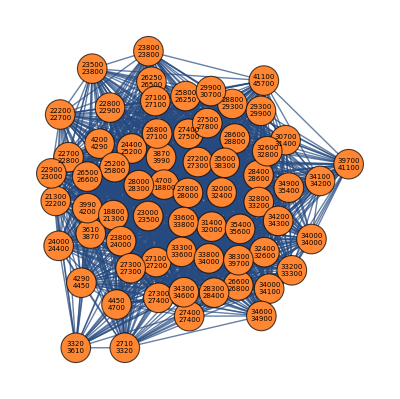
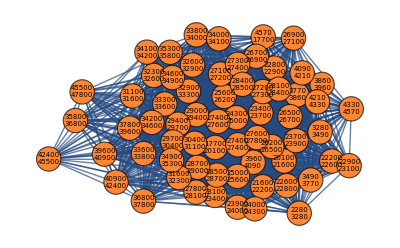
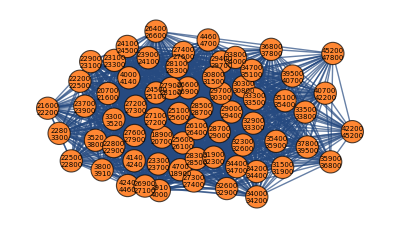
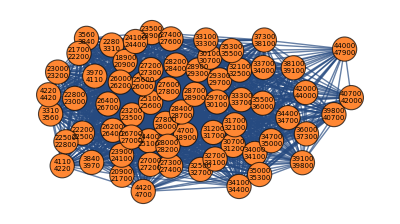
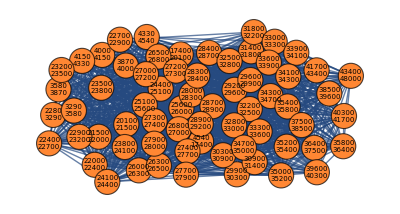
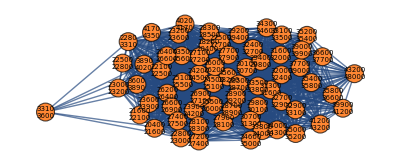
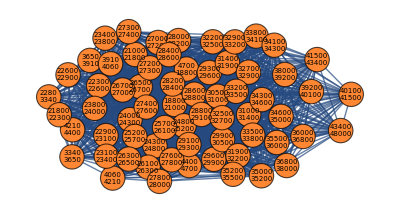
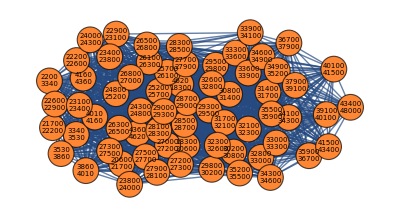
{{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

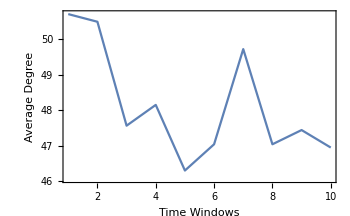
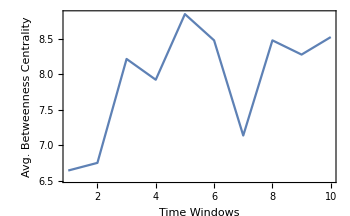
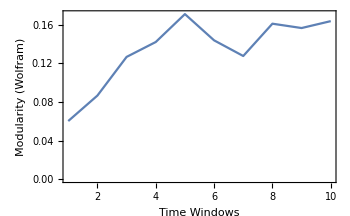
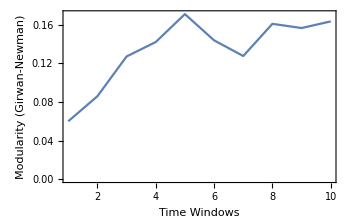

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[11,38,10];]
```

{2015.52,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedbucket[[1]][[i]],weightdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Red],{i,Range@10}];
```

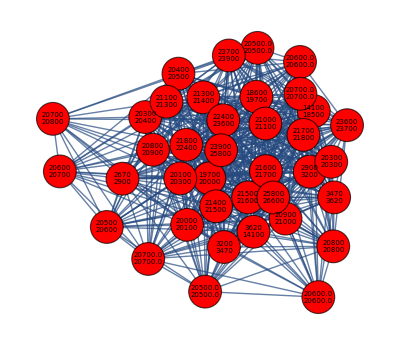
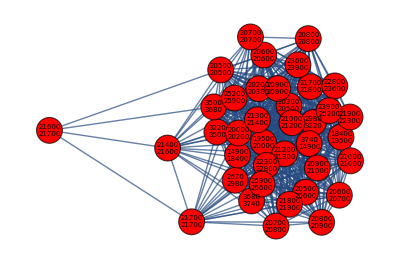
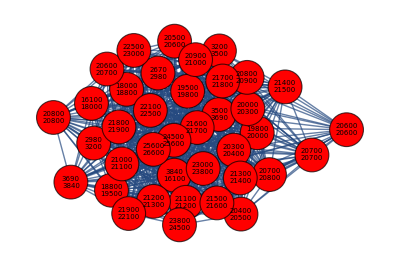
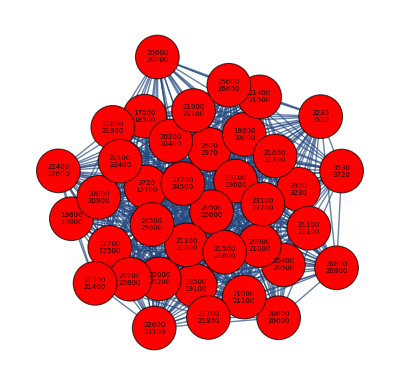
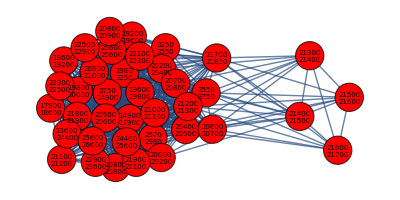
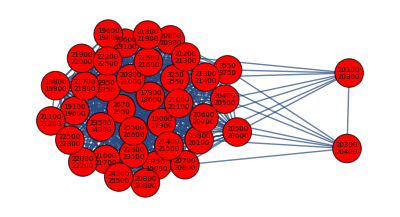
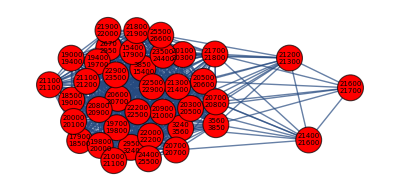
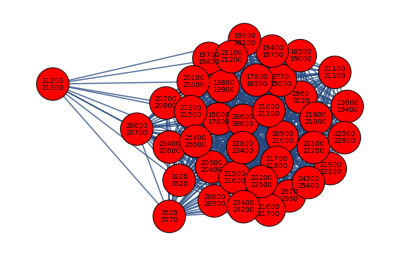
{{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

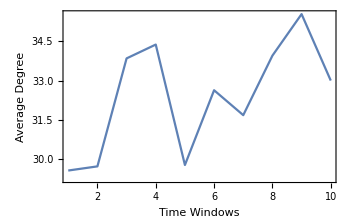
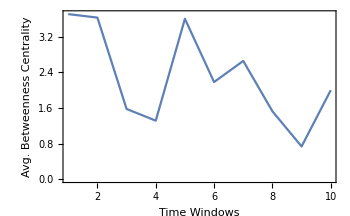
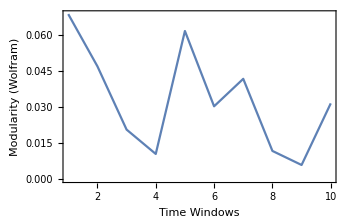
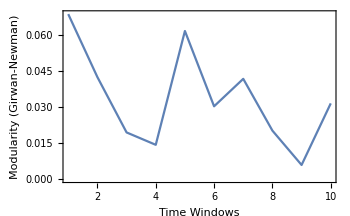

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Modeling Works with OR Methods

FBA Model Reproducing from Kauffman et al. 2003

```mathematica
stochmatrix={{-1,-1,1,0,1,0,0},{1,0,0,1,0,-1,0},{0,1,-1,-1,0,0,-1}};
objectivefunc1={2,0,0,1,0,0,0};
objectivefunc2={1,0,0,2,0,0,0};
boundaries={{0,Infinity},{0,Infinity},{0,0},{0,Infinity},{0,1},{0,2},{0,0}};
steadystatevector={{0,0},{0,0},{0,0}};
Vvector={v1,v2,v3,v4,b1,b2,b3};
```

stochmatrix . Vvector = steadystatevector
-objectivefunc ∈ solution space within boundaries

```mathematica
Print["1st objective function solution vector: ",Vvector1=LinearProgramming[-objectivefunc1,stochmatrix,steadystatevector,boundaries]]
Print["2nd objective function solution vector: ",Vvector2=LinearProgramming[-objectivefunc2,stochmatrix,steadystatevector,boundaries]]
```

1st objective function solution vector: {1,0,0,0,1,1,0}

2nd objective function solution vector: {0,1,0,1,1,1,0}

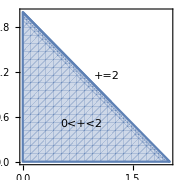

```mathematica
Show[RegionPlot[0<+<2,{,0,2},{,0,2},Frame->True,PlotLabels->Placed["0<+<2",{0.8,0.5}],FrameLabel->{"",""}],Plot[-+2,{,0,1.2},Frame->True,PlotLabels->Placed["+=2",{1.1,1}]],PlotRange->All,ImageSize->Small]
```

```mathematica
FindMaximum[{2v4+b1,-v1-v2+v3+b1==0&&v1+v4-b2==0&&v2-v3-v4-b3==0&&0≤v1+v2≤1&&0≤v1+v4≤2&&v2-v4==0&&0≤b1≤1&&0≤b2≤2&&b3==0&&v1≥0&&v2≥0&&v3==0&&v4≥0},{v1,v2,v3,v4,b1,b2,b3}]
```

{3.,{v1→0.,v2→1.,v3→0.,v4→1.,b1→1.,b2→1.,b3→0.}}

Implementation for the Thesis Dataset